# N-Channel Square Well Model (with energy normalized functions)

NPM

## Setup the Riccati functions and their derivatives

Use energy normalized functions (assuming μ=1/2 is the reduced mass)

```mathematica
Clear[L]
```

```mathematica
f[L_,k_,r_]=Simplify[√(1/(π k))√((π k)/2 r)BesselJ[L+1/2,k r]];
```

```mathematica
df[L_,k_,r_]=Simplify[D[f[L,k,r],r]];(*r-derivative*)
```

```mathematica
dfdk[L_,k_,r_]=Simplify[D[f[L,k,r],k]];(*k-derivative*)
```

```mathematica
ddfdk[L_,k_,r_]=FullSimplify[D[df[L,k,r],k]];
```

```mathematica
g[L_,k_,r_]=Simplify[√(1/(π k))√((π k)/2 r)BesselY[L+1/2,k r]];
```

```mathematica
dg[L_,k_,r_]=Simplify[D[g[L,k,r],r]];
```

```mathematica
dgdk[L_,k_,r_]=Simplify[D[g[L,k,r],k]];
```

```mathematica
ddgdk[L_,k_,r_]=FullSimplify[D[dg[L,k,r],k]];
```

I’ll multiply the decaying function by a constant to rescale it for the strongly closed channels.

```mathematica
gb[L_,κ_,r_]=√(2/π κ r)BesselK[L+1/2,κ r]Exp[κ Rshift]/.Rshift->1;
```

```mathematica
dgb[L_,κ_,r_]=Simplify[D[gb[L,κ,r],r]];
```

```mathematica
dgbdκ[L_,κ_,r_]=Simplify[D[gb[L,κ,r],κ]];
```

```mathematica
ddgbdκ[L_,κ_,r_]=Simplify[D[dgb[L,κ,r],κ]];
```

```mathematica
fb[L_,κ_,r_]=√(2/π κ r)BesselI[L+1/2,κ r];
```

```mathematica
dfb[L_,κ_,r_]=Simplify[D[fb[L,κ,r],r]];
```

```mathematica
dfbdκ[L_,κ_,r_]=Simplify[D[fb[L,κ,r],κ]];
```

```mathematica
ddfbdκ[L_,κ_,r_]=Simplify[D[dfb[L,κ,r],κ]];
```

The background scattering phase shift (due to the open channel only)

```mathematica
BG[vopen_,ϵ_]:=Module[{y,δ,td,kin,kout},
kin = √(ϵ+vopen);
kout=√ϵ;
y=df[0,kin ,1]/f[0,kin, 1];
td=(df[0,kout ,1]-y f[0,kout, 1])/(dg[0,kout, 1]-y g[0,kout, 1]);
δ=ArcTan[td]
]
```

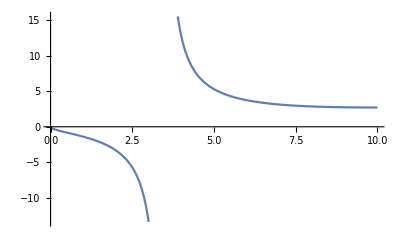

```mathematica
Plot[Tan[BG[10,ϵ]],{ϵ,0,10}]
```

The tri-diagonal potential matrix:

```mathematica
SetupPotentialTriDiag[NumChan_,D0_,Δ_,Cij_]:=
Module[{i,j,ϵthresh,Λvals,U,V,UC,ΛC,VC},
ϵthresh=Table[If[i==NumChan,0,Δ],{i,1,NumChan}];
V=Table[If[i==j,-D0,(KroneckerDelta[i,j-1]+ KroneckerDelta[i,j+1])Cij],{i,1,NumChan},{j,1,NumChan}];
Λvals=Simplify[Eigenvalues[V]];
U=Transpose[Table[FullSimplify[Normalize[Eigenvectors[V][[n]]]],{n,1,NumChan}]];
VC=V[[1;;NumChan-1,1;;NumChan-1]];
ΛC=Simplify[Eigenvalues[VC]];
UC=Transpose[Table[FullSimplify[Normalize[Eigenvectors[VC][[n]]]],{n,1,NumChan-1}]];
{Λvals,U,ϵthresh,V,UC,ΛC}
]
```

Setup a potential matrix with resonance at position “eoffset”. control the width with coupling “Cij”.  Only include couplings between the open channel and each closed channels.

```mathematica
SetupPotentialOpenClosed[NumChan_,Dopen_,Δ_,Cij_,eoffset_]:=
Module[{i,j,ϵthresh,Λvals,U,V,n,r0,v0,VC,UC,ΛC},
n=1;r0=1;
ϵthresh=Table[If[i==NumChan,0,Δ+eoffset[[i]]],{i,1,NumChan}];
v0=v0/.FindRoot[√(v0-Δ) Cos[r0 √(v0-Δ)]+√Δ Sin[r0 √(v0-Δ)],{v0,1/2((n-1/2)^2+n^2)π^2+Δ}];
V=Table[0,{i,1,NumChan},{j,1,NumChan}];
Do[V[[i,i]]=-v0+Δ+eoffset[[i]],{i,1,NumChan-1}];
V[[NumChan,NumChan]]=-Dopen;
Do[
V[[i,NumChan]]=Cij;
V[[NumChan,i]]=Cij,
{i,1,NumChan-1}
];
Λvals=Simplify[Eigenvalues[V]];
U=Transpose[Table[FullSimplify[Normalize[Eigenvectors[V][[n]]]],{n,1,NumChan}]];
VC=V[[1;;NumChan-1,1;;NumChan-1]];
ΛC=Simplify[Eigenvalues[VC]];
UC=Transpose[Table[FullSimplify[Normalize[Eigenvectors[VC][[n]]]],{n,1,NumChan-1}]];
{Λvals,U,ϵthresh,V,UC,ΛC}
]
```

A simple two-channel potential:

```mathematica
Setup2channelpot[Deptho_,Depthc_,Δ_,c_]:=
Module[{i,j,ϵthresh,Λvals,U,V,r0,v0,VC,UC,ΛC},
r0=1;
ϵthresh=Table[0,{i,1,2}];
ϵthresh[[1]]=Δ;
V=Table[0,{i,1,2},{j,1,2}];
V[[1,1]]=-Depthc;
V[[2,2]]=-Deptho;
V[[1,2]]=c;
V[[2,1]]=c;
Λvals=Simplify[Eigenvalues[V]];
U=Transpose[Table[FullSimplify[Normalize[Eigenvectors[V][[n]]]],{n,1,2}]];
VC=V[[1;;1,1;;1]];
ΛC=Simplify[Eigenvalues[VC]];
UC=Transpose[Table[FullSimplify[Normalize[Eigenvectors[VC][[n]]]],{n,1,1}]];
{Λvals,U,ϵthresh,V,UC,ΛC}
]
```

Functions for the interior solutions

```mathematica
ϕ[L_,λsqr_,Energy_,r_]:=If[Energy-λsqr>0,f[L,√(Energy-λsqr),r],fb[L,√(λsqr-Energy),r]];
dϕ[L_,λsqr_,Energy_,r_]:=If[Energy-λsqr>0,df[L,√(Energy-λsqr),r],dfb[L,√(λsqr-Energy),r]];
```

```mathematica
dϕdE[L_,λsqr_,Energy_,r_]:=Module[{k,κ},
k=√(Energy-λsqr);
κ=√(λsqr-Energy);
If[Energy-λsqr>0,dfdk[L,k,r] 1/(2k),dfbdκ[L,κ, r](-1/(2κ))]]
ddϕdE[L_,λsqr_,Energy_,r_]:=Module[{κ,k},
k=√(Energy-λsqr);
κ=√(λsqr-Energy);
If[Energy-λsqr>0,ddfdk[L,k,r] 1/(2k),ddfbdκ[L,κ, r](-1/(2κ))]]
```

Module to make the interior Φ_ij

```mathematica
MakeΦMat[NumChan_,L_,Λ_,U_,Energy_,r_]:=Module[
{Φ,dΦ,i,j,dΦdE,ddΦdE},
Φ=Table[U[[i,j]]ϕ[L,Λ[[j]],Energy,r],{i,1,NumChan},{j,1,NumChan}];
dΦ=Table[U[[i,j]]dϕ[L,Λ[[j]],Energy,r],{i,1,NumChan},{j,1,NumChan}];
dΦdE=Table[U[[i,j]]dϕdE[L,Λ[[j]],Energy,r],{i,1,NumChan},{j,1,NumChan}];
ddΦdE=Table[U[[i,j]]ddϕdE[L,Λ[[j]],Energy,r],{i,1,NumChan},{j,1,NumChan}];
{Φ,dΦ,dΦdE,ddΦdE}
]
```

Setup the matrix for the linear solve.

```mathematica
SetupABMatNew[NumChan_,NumOpen_,ϵthresh_,Φ_,dΦ_,dΦdE_,ddΦdE_,L_,r_,Energy_]:=
Module[{i,j,SizeAB,κc,ko,NumClosed,ABmat,bvec,ABmatdE},
SizeAB=2 NumChan+1;
NumClosed=NumChan-NumOpen;
ABmat=Table[0,{i,1,SizeAB},{j,1,SizeAB}];
ABmatdE=Table[0,{i,1,SizeAB},{j,1,SizeAB}];
(*Closed Channels Interior*)

Do[
ABmat[[2 i-1,1;;NumChan]]=Φ[[i]];
ABmat[[2 i,1;;NumChan]]=dΦ[[i]];
ABmatdE[[2i-1,1;;NumChan]]=dΦdE[[i]];
ABmatdE[[2i,1;;NumChan]]=ddΦdE[[i]];,
{i,1,NumClosed}
];
(*Open Channel Interior*)
ABmat[[2 NumChan-1,1;;NumChan]]=Φ[[NumChan]];
ABmat[[2 NumChan,1;;NumChan]]=dΦ[[NumChan]];
ABmatdE[[2NumChan-1,1;;NumChan]]=dΦdE[[NumChan]];ABmatdE[[2NumChan,1;;NumChan]]=ddΦdE[[NumChan]];

(*Closed Channels Exterior*)
Do[
κc=√(ϵthresh[[i]]-Energy);
ABmat[[2i-1,NumChan+i]]=-gb[L,κc ,r];
ABmat[[2 i,NumChan+i]]=-dgb[L,κc ,r] ;
ABmatdE[[2i-1,NumChan+i]]=-dgbdκ[L,κc,r](-1/(2κc)) ;
ABmatdE[[2 i,NumChan+i]]=-ddgbdκ[L,κc ,r](-1/(2κc));,
{i,1,NumClosed}];

(*Open Channel Exterior*)
ko=√(Energy-ϵthresh[[NumChan]]);
ABmat[[2 NumChan-1,NumChan+NumClosed+1]]=-f[L,ko ,r];
ABmat[[2 NumChan-1,NumChan+NumClosed+2]]=g[L,ko ,r];
ABmat[[2 NumChan,NumChan+NumClosed+1]]=-df[L,ko ,r];
ABmat[[2 NumChan,NumChan+NumClosed+2]]=dg[L,ko ,r];

ABmatdE[[2 NumChan-1,NumChan+NumClosed+1]]=-dfdk[L,ko ,r] 1/(2ko);
ABmatdE[[2 NumChan-1,NumChan+NumClosed+2]]=dgdk[L,ko ,r] 1/(2ko);
ABmatdE[[2 NumChan,NumChan+NumClosed+1]]=-ddfdk[L,ko, r] (1/(2ko));
ABmatdE[[2 NumChan,NumChan+NumClosed+2]]=ddgdk[L,ko ,r] (1/(2ko));
(* Pick the open channel cosine amplitude to be 1 *)
(*ABmat[[SizeAB,NumChan+NumClosed+1]]=1; *)
(* Pick the first closed channel to have Subscript[a, 1]=1 *)
ABmat[[SizeAB,NumChan+1]]=1; 
bvec=Table[0,{i,SizeAB}];
bvec[[SizeAB]]=1;

{ABmat,bvec,ABmatdE}
]
```

A module to calculate observables from the solution to the linear equation

```mathematica
SolutionData[NumChan_,NumOpen_,ϵthresh_,sols_,solsE_,L_,r_,Energy_]:=Module[
{ascat,sigma,aclose,aLsqr,norm,δOverπ,coef,σ,i,j,δ,SizeAB,tandel,dsdE,timedelay},

SizeAB=2NumChan+1;
tandel=sols[[SizeAB]]/sols[[SizeAB-1]];
ascat=-tandel/√Energy;
norm=1/(√(sols[[SizeAB-1]]^2+sols[[SizeAB]]^2));
δ=ArcTan[tandel];
δOverπ=δ/π;
aclose=sols[[NumChan+1;;2NumChan-1]];
coef=sols[[1;;NumChan]];

aLsqr=Sin[δ]^2;
σ=(4π aLsqr)/Energy;
dsdE=solsE[[SizeAB]];
timedelay=2 Cos[δ]^2(-1/sols[[SizeAB-1]]^2 solsE[[SizeAB-1]]sols[[SizeAB]]+1/sols[[SizeAB-1]] dsdE);
{ascat,δOverπ,aLsqr,norm,timedelay}]
```

A module to solve the linear problem at one energy point

```mathematica
EnergyPoint[NumChan_,NumOpen_,L_,rmatch_,Λ_,U_,ϵth_,Energy_]:=Module[
{Φ,dΦ,dΦdE,ddΦdE,AB,ABdE,b,sols,solsE,data,cvec},
{Φ,dΦ,dΦdE,ddΦdE}=MakeΦMat[NumChan,L,Λ,U,Energy,rmatch];
{AB,b,ABdE}=SetupABMatNew[NumChan,NumOpen,ϵth,Φ,dΦ,dΦdE,ddΦdE,L,rmatch,Energy];
sols=LinearSolve[AB,b];
cvec =- ABdE.sols;
solsE=LinearSolve[AB,cvec];
data=SolutionData[NumChan,NumOpen,ϵth,sols,solsE,L,rmatch,Energy];
data
]
```

The transcendental equation for the bound-state sector...

```mathematica
BSTEQ[Energy_,Λ_,U_,L_,ϵth_,rmatch_,NumClosed_]:=Module[{i,j,Gmat,Φ,dΦ,dΦdE,ddΦdE,κ,BSMAT},
Gmat=Table[0,{i,1,NumClosed},{j,1,NumClosed}];
Do[(κ=√(ϵth[[i]]-Energy);Gmat[[i,i]]=dgb[L, κ ,rmatch]/gb[L,κ,rmatch]),{i,1,NumClosed}];
{Φ,dΦ,dΦdE,ddΦdE}=MakeΦMat[NumClosed,L,Λ,U,Energy,rmatch];
BSMAT=dΦ-Gmat.Φ;
Det[BSMAT]
]
```

Set up the parameters for the “simple example”

```mathematica
NCHAN=3;
Dopen=50.0;
Δ=200.0;
cij=5.0;
D0=50.0;
NumOpen=1;
L=0;
rmatch=1.0;
```

```mathematica
{Λ,U,ϵth,V,UC,ΛC}=SetupPotentialTriDiag[NCHAN,D0,Δ,cij];
emin = 0.1;
emax =199.9;
nume=5000;
Egrid=Table[ϵ,{ϵ,emin,emax,(emax-emin)/nume}];
```

```mathematica
padding={{100,45},{80,0}};
imgsize={600,300};
yrange=All;
xrange={0,200};
aspctratio=Full;1/GoldenRatio;
```

InterpolatingFunction[{{0.1, 199.9}}, <>]

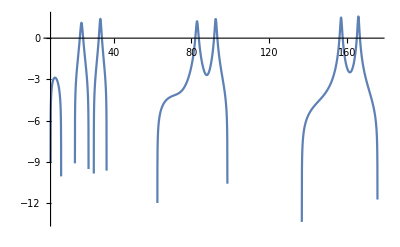

```mathematica
DataTable=Table[{ϵ,EnergyPoint[NCHAN,NumOpen,L,rmatch,Λ,U,ϵth,ϵ]},{ϵ,Egrid}];
δtable=Table[{Egrid[[i]],π DataTable[[i,2,2]]},{i,1,Length[Egrid]}];
Do[If[δtable[[i,2]]-δtable[[i+1,2]]≥0.2,Do[δtable[[j,2]]=δtable[[j,2]]+π,{j,i+1,nume}]],{i,1,nume}]
Do[If[δtable[[i,2]]-δtable[[i+1,2]]≤-0.5,Do[δtable[[j,2]]=δtable[[j,2]]-π,{j,i+1,nume}]],{i,1,nume}]
δinterp=Interpolation[δtable]
Plot[Log[2D[δinterp[x],x]]/.x->ϵ,{ϵ,0.1,199},PlotRange->All]
```

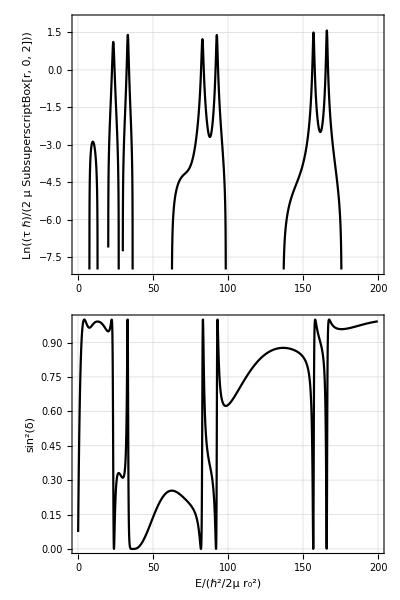

```mathematica
palnew=ListPlot[Table[{Egrid[[i]],DataTable[[i,2,3]]},{i,1,nume}],Joined->True,PlotStyle->{{Black},{Red,Dotted}},Frame->True,FrameLabel->{"E/(ℏ^2/2μ r_0^2)",TraditionalForm[Sin[δ]^2]},LabelStyle->{16},PlotRange->{xrange,yrange},GridLines->Automatic,ImageSize->{600,300},ImagePadding->{{100,45},{60,8}},AspectRatio->aspctratio,FrameTicks->{Automatic,Automatic}];
pdetnew=Plot[BSTEQ[Energy,ΛC,UC,0,ϵth,rmatch,NCHAN-1],{Energy,0,ϵth[[1]]},PlotStyle->Black,Frame->True,LabelStyle->{16},PlotRange->{xrange,{-10^-50,10^-50}},AspectRatio->50/1000,ImageSize->{600,50},PlotRangeClipping->False,ImagePadding->{{100,45},{0,20}},FrameTicks->{None,None},ImageMargins->0,Axes->False];
ptdnew=ListPlot[Table[{Egrid[[i]],Log[DataTable[[i,2,5]]]},{i,1,nume}],Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{(*"E/(ℏ^2/2μr_0^2)"*)None,"Ln((τ ℏ)/(2  μ SubsuperscriptBox[r, 0, 2]))"},LabelStyle->{16},PlotRange->{xrange,{-8,2}},GridLines->Automatic,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},ImageSize->{600,250},ImagePadding->{{100,45},{8,8}},AspectRatio->aspctratio,ImageMargins->0];
p1=Grid[{{pdetnew},{ptdnew},{palnew}},Spacings->0]
```